# Initial conditions

```mathematica
(*we keep the same values for unrescaled quantities as the numerical solution notebook for matching*)
```

```mathematica
(*Keep m1 > m2. Set Rinit and Pinit so that you start at the point of closest distance. Keep PN parameter small: ϵ ->0, P ->0, 1/R -> 0,  spins/(orb. ang. momentum) -> 0*)

m1=2.5 ;  m2=1;G=1;   ϵ= 0.005; c = 1/(√ϵ)   ; spinSuppressFac = ϵ; tfin = 100000;
M = m1+m2 ;  μ = m1 m2/M ;
δ1=2 m1 m2/M^2 (1+3/4 m2/m1)  ;δ2=2 m2 m1/M^2 (1+3/4 m1/m2) ; 
kGoldstein = G M μ ;
```

```mathematica
Rinit=1{ 3,0,0};
Pinit=1{0,-1,0};
S1init={0,1,1}/kGoldstein spinSuppressFac;     
S2init={1,-0.3,0}/kGoldstein spinSuppressFac;
S1ninit = Norm[S1init];
S2ninit = Norm[S2init];
rinit=Rinit/(G M)     ;     pinit=Pinit/μ ;
Linit=Cross[rinit,pinit] ;     Lninit = Norm[Linit] ;
(*Prepare  a sign function for later use in solution*)

If [ δ2/(c^2 Norm[rinit]^3 S1ninit Lninit)Linit.Cross[S1init, S2init]   > 0, sign =1, sign =-1 ] ;
```

# Un-rescaled/rescaled quantities

```mathematica
R = {Rx, Ry,Rz} ; P ={Px,Py,Pz};
S1= {S1x, S1y,S1z} ;    S2= {S2x, S2y,S2z} ;
S1n = Norm[S1] ;     S2n = Norm[S2] ;

Seff= (δ1 S1+ δ2 S2);
r=R/(G M);       p=P/μ;
L=Cross[r,p] ;(*Conserved quantities defined in terms of scaled variables*) 
Ln=Norm[L] ;
Jn=Norm[L+S1+S2];
SeffL= Seff.L ;
```

```mathematica
(*Evaluating σ1 and σ2*)
{Rx,Ry,Rz} = Rinit  ;
{Px,Py,Pz}=Pinit  ;
{S1x,S1y,S1z} = S1init ; 
{S2x,S2y,S2z} = S2init  ;

σ1=(S1.S2)/(S1n S2n) -Ln/S2n(δ1-δ2)/δ2(S1.L)/(Ln S1n) ;   (*σ1=Cos γ -L/S2(Q1-Q2)/Q2 Cos κ1 *)
σ2= (S2.L)/(Ln S2n) + (δ1 S1n)/(δ2 S2n)(S1.L)/(Ln S1n) ;           (*σ2= Cos κ2 +(Q1 S1)/(Q2 S2) Cos κ1*)
Enwt=(P.P)/(2 μ) -(G μ M)/Norm[R];(*Newtonian expression for energy*)
Lun=Norm[Cross[R,P]];  (*norm of unscaled ang momentum*)
e = (1 + 2 Enwt  Lun^2/(μ kGoldstein^2))^(1/2) ;(*Newtonian eccentricity in unrescaled variables*)
aUnrescaled= -kGoldstein/(2 Enwt) ;
a = aUnrescaled/(G M) ;
n = ((Ln/(a (1-e^2)^(1/2)))^3)/(G M) ;   (*unrescaled*)
```

# Cubic equation

```mathematica
A=2 Ln S1n δ1 (δ2-δ1);cubiceq=A x^3 -(Ln^2 (δ1-δ2)^2+2 δ2 Ln σ2 S2n  (δ2-δ1)+S1n^2 δ1^2+2 δ1 δ2 σ1 S1n S2n +δ2^2  S2n^2  )x^2+ (2  δ2 S2n (Ln σ1(δ2-δ1) +σ2( δ1 S1n+ δ2 σ1 S2n) )) x+-S2n^2 δ2^2 (σ1^2+σ2^2-1);(*=A(x -x1)(x -x2)(x -x3)*)
```

```mathematica
(*evaluate the cubic and find the roots*)
rtsol=Solve[cubiceq==0,x] ;
x2=x/.rtsol[[1]] ; 
x3=x/.rtsol[[2]] ;
x1=x/.rtsol[[3]];
{x2, x3, x1} = Sort[{x2, x3, x1}] ;
Clear[Rx, Ry, Rz, Px, Py, Pz, S1x, S1y, S1z, S2x, S2y, S2z, m1, m2]
```

# Solution of Cos[κ_1]

```mathematica
βe = e/(1+(1-e^2)^(1/2)) ;
ν = u + 2 ArcTan[ (βe Sin[u])/(1-βe Cos[u])]      ;(*same as ν= 2 ArcTan[√((1+e)/(1-e)) Tan[u/2]] but without the ArcTan issues*)

β = ((x3-x2)/(x1-x2))^(1/2);
α =  sign 2/(√(A(x1-x2)))EllipticF[ArcSin[√(((S1init.Linit)/(Lninit S1ninit)-x2)/(x3-x2))],β^2]   ;
Υ = 1/2 √(A(x1-x2))(α+(ν + e Sin[ν])/(c^2 Ln^3)) ;
coskp1=x2+(x3-x2)JacobiSN[Υ,β^2]^2;
```

```mathematica
(*Evaluate coskp1*)
{Rx,Ry,Rz} = Rinit  ;
{Px,Py,Pz}=Pinit  ;
{S1x,S1y,S1z} = S1init ; 
{S2x,S2y,S2z} = S2init  ; 

fr[λ_?NumericQ]:=FindRoot[n λ == u - e Sin[u],{u,0}];
```

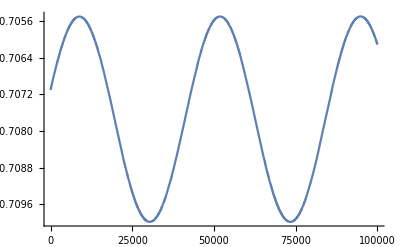
```mathematica
fcoskp1[λ_?NumericQ]:=coskp1/.fr[λ];
p1 =    -Graphics- ;
p2=Plot[fcoskp1[λ],{λ,0,tfin},PlotStyle->Red];
Show[p2,p1, PlotRange->All]


(*Clear[Rx, Ry, Rz, Px, Py, Pz, S1x, S1y, S1z, S2x, S2y, S2z, m1, m2]
*)
```

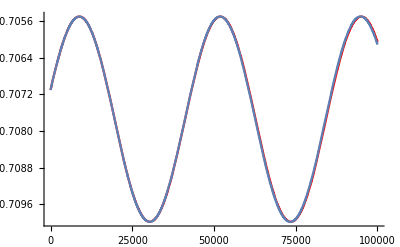

```mathematica
Quit[];
```